```mathematica
(* constants *)
SubMinus[c] = 6000.;
SubPlus[c]  = 1500;
SubMinus[ρ] = 3100.;
SubPlus[ρ] = 1000.;
ω = 2100.;

a = (SubMinus[ρ]/SubPlus[ρ])^2;
b = (SubPlus[c]/SubMinus[c])^2;
L0 = 0.;
p0 =√((ω^2 + L0)/SubPlus[c]^2) ;

getTrajAndPhase[x1in_, x2in_,bottomFunc_, modeNum_, timeTo_] := (
bot[x1_,x2_] := bottomFunc[x1, x2];
q= t /.FindRoot[{t^2 (a*(Cot[t])^2 + 1) == (bot[x1in, x2in])^2 p0^2(1 - b)}, {t, 3.14 modeNum, 3.142 (modeNum - 1), 3.141 modeNum}];
Subscript[p, abs] := Sqrt[p0^2 - (q/bot[x1in, x2in])^2];

{x1sol, x2sol,p1sol, p2sol} =ParametricNDSolve[{Subscript[x, 1]'[t]==(2 ((SubMinus[c] SubMinus[ρ])/(SubPlus[c] SubPlus[ρ]))^2 Cos[bot[Subscript[x, 1][t], Subscript[x, 2][t]] √(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2))]/((Sin[bot[Subscript[x, 1][t], Subscript[x, 2][t]] √(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2))])^3) 1/(√(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2))) bot[Subscript[x, 1][t], Subscript[x, 2][t]] - 2  (p0^2 (1/b - 1))/((p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2))^2)) Subscript[p, 1][t],
Subscript[x, 2]'[t]==(2 ((SubMinus[c] SubMinus[ρ])/(SubPlus[c] SubPlus[ρ]))^2 Cos[bot[Subscript[x, 1][t], Subscript[x, 2][t]] √(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2))]/((Sin[bot[Subscript[x, 1][t], Subscript[x, 2][t]] √(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2))])^3) 1/(√(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2))) bot[Subscript[x, 1][t], Subscript[x, 2][t]] - 2  (p0^2 (1/b - 1))/((p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2))^2))Subscript[p, 2][t],
Subscript[p, 1]'[t]==(2 ((SubMinus[c] SubMinus[ρ])/(SubPlus[c] SubPlus[ρ]))^2 Cos[bot[Subscript[x, 1][t], Subscript[x, 2][t]] √(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2))]/((Sin[bot[Subscript[x, 1][t], Subscript[x, 2][t]] √(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2))])^3) √(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2)) (Derivative[1,0][bot][Subscript[x, 1][t],Subscript[x, 2][t]])),     Subscript[p, 2]'[t]==(2 ((SubMinus[c] SubMinus[ρ])/(SubPlus[c] SubPlus[ρ]))^2 Cos[bot[Subscript[x, 1][t], Subscript[x, 2][t]] √(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2))]/((Sin[bot[Subscript[x, 1][t], Subscript[x, 2][t]] √(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2))])^3) √(p0^2 - ((Subscript[p, 1][t])^2 + (Subscript[p, 2][t])^2)) (Derivative[0,1][bot][Subscript[x, 1][t],Subscript[x, 2][t]])),
Subscript[x, 1][0]==x1in, Subscript[x, 2][0]==x2in, Subscript[p, 1][0]==Subscript[p, abs] Cos[θ], Subscript[p, 2][0] == Subscript[p, abs] Sin[θ]},
{Subscript[x, 1], Subscript[x, 2], Subscript[p, 1], Subscript[p, 2]},{t,0.,timeTo},{θ}, Method->{"TimeIntegration"->"ExplicitRungeKutta"}];


Subscript[x, 1][θ_, t_] := (Subscript[x, 1][θ]/.x1sol)[t];
Subscript[x, 2][θ_, t_] := (Subscript[x, 2][θ]/.x2sol)[t];
Subscript[p, 1][θ_, t_] := (Subscript[p, 1][θ]/.p1sol)[t];
Subscript[p, 2][θ_, t_] := (Subscript[p, 2][θ]/.p2sol)[t];
Subscript[dx, 1][θ_, t_] := (2 ((SubMinus[c] SubMinus[ρ])/(SubPlus[c] SubPlus[ρ]))^2 Cos[bot[Subscript[x, 1][θ, t], Subscript[x, 2][θ, t]] √(p0^2 - ((Subscript[p, 1][θ, t])^2 + (Subscript[p, 2][θ, t])^2))]/((Sin[bot[Subscript[x, 1][θ, t], Subscript[x, 2][θ, t]] √(p0^2 - ((Subscript[p, 1][θ, t])^2 + (Subscript[p, 2][θ, t])^2))])^3) 1/(√(p0^2 - ((Subscript[p, 1][θ, t])^2 + (Subscript[p, 2][θ, t])^2))) bot[Subscript[x, 1][θ, t], Subscript[x, 2][θ, t]] - 2  (p0^2 (1/b - 1))/((p0^2 - ((Subscript[p, 1][θ, t])^2 + (Subscript[p, 2][θ, t])^2))^2)) Subscript[p, 1][θ, t];

Subscript[dx, 2][θ_, t_] := (2 ((SubMinus[c] SubMinus[ρ])/(SubPlus[c] SubPlus[ρ]))^2 Cos[bot[Subscript[x, 1][θ, t], Subscript[x, 2][θ, t]] √(p0^2 - ((Subscript[p, 1][θ, t])^2 + (Subscript[p, 2][θ, t])^2))]/((Sin[bot[Subscript[x, 1][θ, t], Subscript[x, 2][θ, t]] √(p0^2 - ((Subscript[p, 1][θ, t])^2 + (Subscript[p, 2][θ, t])^2))])^3) 1/(√(p0^2 - ((Subscript[p, 1][θ, t])^2 + (Subscript[p, 2][θ, t])^2))) bot[Subscript[x, 1][θ, t], Subscript[x, 2][θ, t]] - 2  (p0^2 (1/b - 1))/((p0^2 - ((Subscript[p, 1][θ, t])^2 + (Subscript[p, 2][θ, t])^2))^2)) Subscript[p, 2][θ, t];

phase[θ_, t_] := Integrate[Subscript[p, 1][θ, t] Subscript[dx, 1][θ, tau] + Subscript[p, 2][θ, tau] Subscript[dx, 2][θ, tau], {tau, 0., t}];
{Subscript[x, 1], Subscript[x, 2], Subscript[p, 1], Subscript[p, 2], phase});

minDepth[modeNum_] := (
minval = First[FindMinimum[{t^2(a (Cot[t])^2 + 1), 3.142 (modeNum - 1) ≤ t ≤ 3.141 modeNum},{t, 3.14 modeNum}]];
(*err = 0.5; (*addition - to be sure of the global mode existence*) *)
dmin = √(minval/ p0^2(1 - b));
dmin);

bottomHole[x1pos_, x2pos_, bottomDepth_, holeDepth_, holeRad_] := (
shapeFunc[x_] := 0.5 (Cos[Pi x] + 1); (*normalized to 1*)
bottomFunc[x1_, x2_] := Piecewise[{{holeDepth * shapeFunc[(√((x1-x1pos)^2+(x2-x2pos)^2))/holeRad], (x1-x1pos)^2+(x2-x2pos)^2≤holeRad^2}, {0.,True}}] + bottomDepth;
(*botTab = Table[{{x1, x2}, bottomPiecewise[x1, x2]}, {x1, -11., 11., 0.1}, {x2, -11., 11., 0.001}];
botTabFlat = Flatten[botTab, 1];
bottomFunc = Interpolation[botTabFlat];*)
bottomFunc);
(*----------------------------------------------------------------------*)
```

```mathematica
bot = bottomHole[0., 0., minDepth[2] + 0.5, 2., 5.];
Plot3D[bot[x1, x2], {x1, -7., 7.}, {x2, -7., 7.}, PlotRange->All, ColorFunction->(ColorData["TemperatureMap"][#3]&), Ticks->None]
```

-Graphics3D-

```mathematica
(* main *)
holeDepth = 2.;
holeRad = 5.;
timeTo= 0.5;
modeNum = 2;
x2in = 0.;
x1in = -2.5;
bottomFunc = bottomHole[0., 0., minDepth[modeNum] + 0.5, holeDepth, holeRad];
{Subscript[x, 1], Subscript[x, 2], Subscript[p, 1], Subscript[p, 2], phase}= getTrajAndPhase[x1in, x2in,bottomFunc, modeNum, timeTo];
(*phaseTab:= Table[{{Subscript[x, 1][θ, t], Subscript[x, 2][θ, t]}, phase[θ, t]}, {θ, 0.05, 2Pi, Pi/25}, {t, 0.001, 0.49, 0.01}];
phaseTabFlat = Flatten[phaseTab, 1];
phaseFunc= Interpolation[phaseTabFlat];*)
(*----------------------------------------------------------------------*)
```

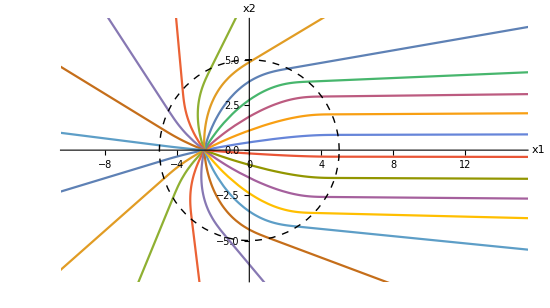

```mathematica
Show[ParametricPlot[Evaluate@Table[{Subscript[x, 1][θ,t], Subscript[x, 2][θ, t]}, {θ,0.2,2Pi, Pi/11}], {t, 0. , timeTo}, PlotRange->{{-10., 15.},{-7., 7.}}, AxesLabel->{x1, x2}],
Graphics[{Thick, Dashed,Circle[{0., 0.}, holeRad]}]]
```

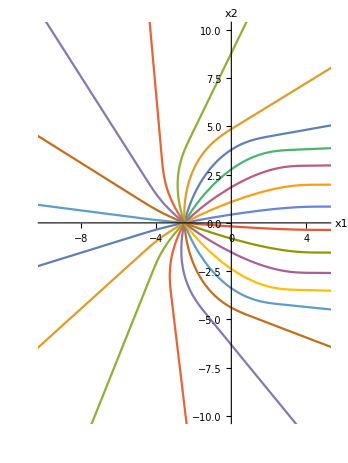

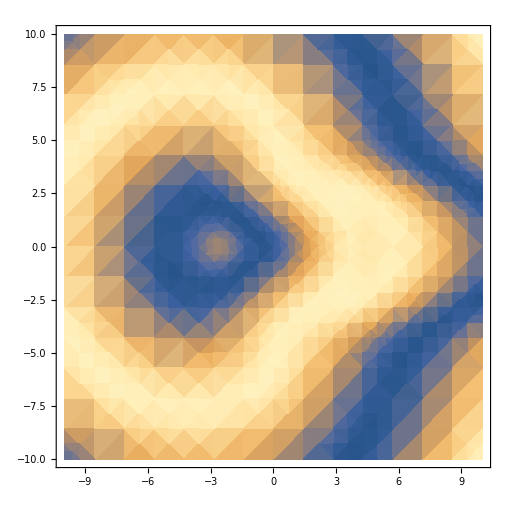

```mathematica
DensityPlot[Sin[phaseFunc[x1, x2]], {x1, -10., 10.}, {x2, -10., 10.}]
```